## 测试

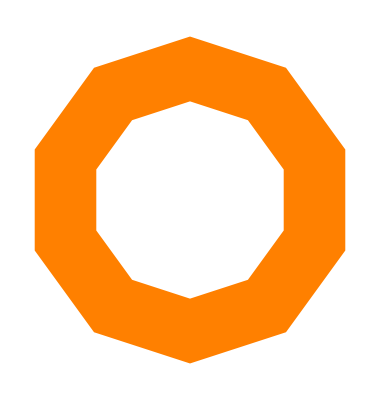

```mathematica
n =10;
region= Polygon[Table[0.8 {Sqrt[4 / (n * Cot[Pi / n])] Sin[
                        2 π k / n], Sqrt[4 / (n * Cot[Pi / n])] Cos[2 π k / n]}, {k, 1, n}]];
areafactor=1/√Area[region];
outerregion=RegionResize[region,Scaled[areafactor]];
rootfactor=
FindRoot[(Area[outerregion]-Area[RegionResize[outerregion,Scaled[interfactor]]])/(Perimeter[outerregion]+Perimeter[RegionResize[outerregion,Scaled[interfactor]]])==0.11,{interfactor,0.5}];
innerregion=RegionResize[outerregion,Scaled[interfactor/.rootfactor[[1]]]];
outerregion=TransformedRegion[outerregion,TranslationTransform[-RegionCentroid@outerregion]];

innerregion=TransformedRegion[innerregion,TranslationTransform[-RegionCentroid@innerregion]];
finalregion=RegionDifference[BoundaryDiscretizeRegion[outerregion],BoundaryDiscretizeRegion[innerregion]];
Graphics[{Orange,finalregion}]
```

## 自动生成形状列表

### 默认颜色/形状列表

```mathematica
colorlistdefault= {RGBColor["#ED2A28"], RGBColor["#3F7CAC"], RGBColor["#F6A13A"
    ], RGBColor["#9E9E49"], RGBColor["#874F9E"], RGBColor["#E96DA8"], RGBColor[
    "#F27C2F"], RGBColor["#2ABCB8"], RGBColor["#D81859"], RGBColor["#367E44"
    ], RGBColor["#4E4E4E"], RGBColor["#FFD700"], RGBColor["#A0522D"]};
regionlistdefault={
RegularPolygon[3],
RegularPolygon[4],
Polygon[Table[0.8 {0.7 Sqrt[4 / (4 * Cot[Pi / 4])] Sin[2 π k / 4], Sqrt[4 / (4* Cot[Pi /4])] Cos[2 π k /4]}, {k, 1,4}]],
RegularPolygon[6],
Disk[],
RegularPolygon[5]};
```

### 自动从区域生成标准大小的空心形状

```mathematica
openregion[region_]:=Module[{innerregion,outerregion,finalshape,areafactor,rootfactor,interfactor,finalregion,compactness},
(*调整外部面积的大小，先面积归一化，再根据紧凑度指数缩放，因为松散的图形视觉效果大*)
areafactor=1/√Area[region];
compactness=((4π Area[region])/Perimeter[region]^2)^0.35;
outerregion=RegionResize[region,Scaled[compactness*areafactor]];
rootfactor=
FindRoot[(Area[outerregion]-Area[RegionResize[outerregion,Scaled[interfactor]]])/(Perimeter[outerregion]+Perimeter[RegionResize[outerregion,Scaled[interfactor]]])==0.11,{interfactor,0.5}];
innerregion=RegionResize[outerregion,Scaled[interfactor/.rootfactor[[1]]]];
outerregion=TransformedRegion[outerregion,TranslationTransform[-RegionCentroid@outerregion]];

innerregion=TransformedRegion[innerregion,TranslationTransform[-RegionCentroid@innerregion]];
finalregion=RegionDifference[BoundaryDiscretizeRegion[outerregion],BoundaryDiscretizeRegion[innerregion]]
];
openregionInner[region_]:=Module[{innerregion,outerregion,finalshape,areafactor,rootfactor,interfactor,finalregion,compactness},
(*调整外部面积的大小，先面积归一化，再根据紧凑度指数缩放，因为松散的图形视觉效果大*)
areafactor=1/√Area[region];
compactness=((4π Area[region])/Perimeter[region]^2)^0.35;
outerregion=RegionResize[region,Scaled[compactness*areafactor]];
rootfactor=
FindRoot[(Area[outerregion]-Area[RegionResize[outerregion,Scaled[interfactor]]])/(Perimeter[outerregion]+Perimeter[RegionResize[outerregion,Scaled[interfactor]]])==0.11,{interfactor,0.5}];
innerregion=RegionResize[outerregion,Scaled[interfactor/.rootfactor[[1]]]];
innerregion=TransformedRegion[innerregion,TranslationTransform[-RegionCentroid@innerregion]];
BoundaryDiscretizeRegion[innerregion]
];
closeregion[region_]:=Module[{innerregion,outerregion,finalshape,areafactor,rootfactor,interfactor,finalregion,compactness},
(*调整外部面积的大小，先面积归一化，再根据紧凑度指数缩放，因为松散的图形视觉效果大*)
areafactor=1/√Area[region];
compactness=((4π Area[region])/Perimeter[region]^2)^0.35;
outerregion=RegionResize[region,Scaled[compactness*areafactor]]
];
```

### 形状列表

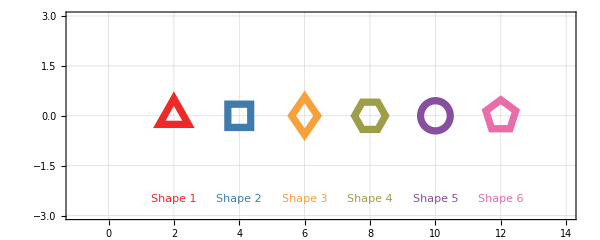

```mathematica
openmarkerlist=openregion/@regionlistdefault;
Graphics[Table[{colorlistdefault[[i]],Translate[openmarkerlist[[i]],{2*i,0}],(*水平位置*)Text["Shape "<>ToString[i],{2*i,-2.5}]     (*添加标签*)},{i,Length[openmarkerlist]}],PlotRange->{{-1,2*Length[openmarkerlist]+2},{-3,3}},Axes->True,GridLines->Automatic,Frame->True,ImageSize->600]
```

### 自动从区域列表+颜色列表生成 List

```mathematica
markerlistcreate[n_,regionlist_,colorlist_,factor_:1 ,openness_:True, coverness_:True]:=Module[{colorlistlength=Length@colorlist,regionlistlength=Length@regionlist,bound,markersizefactor,markerregionlist,innerregionlist},
markerregionlist=If[openness,openregion/@regionlist,closeregion/@regionlist];
If[coverness,innerregionlist=openregionInner/@regionlist];
Table[
bound=RegionBounds[markerregionlist[[Mod[i-1,regionlistlength-1]+1]]]ᵀ;
markersizefactor=bound[[1]]-bound[[2]]//Norm;
{
If[coverness,
Graphics[{colorlist[[Mod[i-1,colorlistlength-1]+1]],
markerregionlist[[Mod[i-1,regionlistlength-1]+1]],
White,innerregionlist[[Mod[i-1,regionlistlength-1]+1]]
}]
,
Graphics[{colorlist[[Mod[i-1,colorlistlength-1]+1]],
markerregionlist[[Mod[i-1,regionlistlength-1]+1]]}]]
,
Scaled[0.02*markersizefactor*factor]},
{i,1,n}]
];
legendlistcreate[n_,regionlist_,colorlist_,factor_:1,openness_:True, coverness_:True]:=Module[{colorlistlength=Length@colorlist,regionlistlength=Length@regionlist,bound,legendsizefactor,markerregionlist},
markerregionlist=If[openness,openregion/@regionlist,closeregion/@regionlist];
Table[
bound=RegionBounds[markerregionlist[[Mod[i-1,regionlistlength-1]+1]]]ᵀ;
legendsizefactor=Abs[(bound[[1]]-bound[[2]])[[1]]];
Graphics[{colorlist[[Mod[i-1,colorlistlength-1]+1]],
markerregionlist[[Mod[i-1,regionlistlength-1]+1]]},ImageSize->15*legendsizefactor*factor],
{i,1,n}]
];
stylecolorlistcreate[n_,colorlist_]:=Module[{colorlistlength=Length@colorlist},
Table[colorlist[[Mod[i-1,colorlistlength-1]+1]],{i,1,n}]];
```

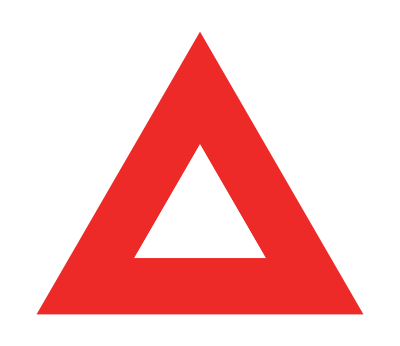
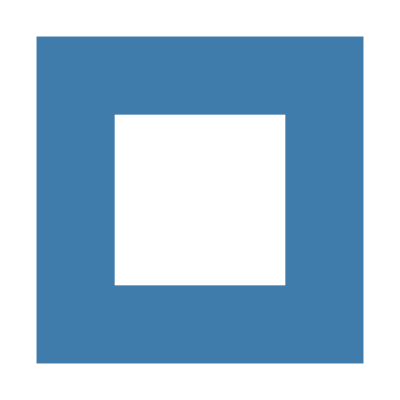
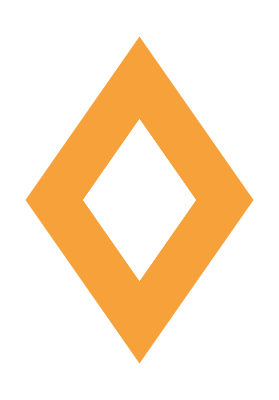
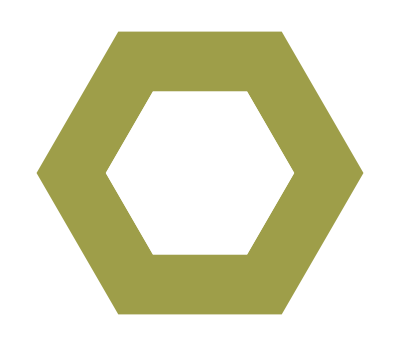
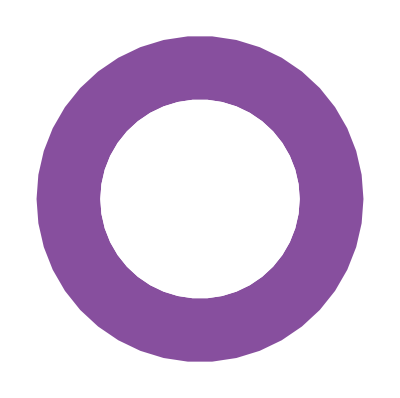
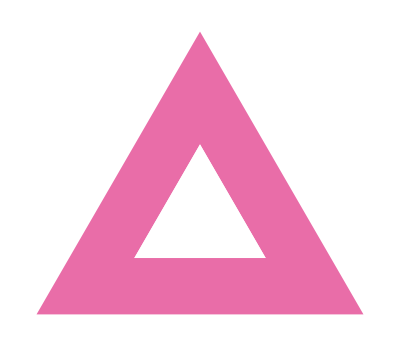
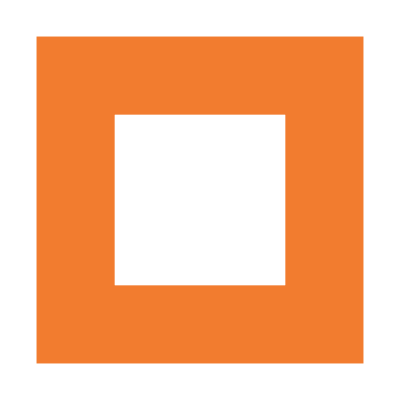
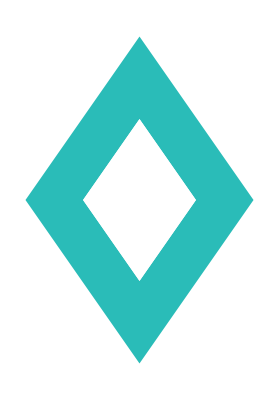
{{-Graphics-,Scaled[0.0337142]},{-Graphics-,Scaled[0.0259912]},{-Graphics-,Scaled[0.0371022]},{-Graphics-,Scaled[0.0317248]},{-Graphics-,Scaled[0.0318708]},{-Graphics-,Scaled[0.0337142]},{-Graphics-,Scaled[0.0259912]},{-Graphics-,Scaled[0.0371022]},{-Graphics-,Scaled[0.0317248]},{-Graphics-,Scaled[0.0318708]}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{RGBColor[0.9294117647058824, 0.16470588235294117, 0.1568627450980392],RGBColor[0.24705882352941178, 0.48627450980392156, 0.6745098039215687],RGBColor[0.9647058823529412, 0.6313725490196078, 0.22745098039215686],RGBColor[0.6196078431372549, 0.6196078431372549, 0.28627450980392155],RGBColor[0.5294117647058824, 0.30980392156862746, 0.6196078431372549],RGBColor[0.9137254901960784, 0.42745098039215684, 0.6588235294117647],RGBColor[0.9490196078431372, 0.48627450980392156, 0.1843137254901961],RGBColor[0.16470588235294117, 0.7372549019607844, 0.7215686274509804],RGBColor[0.8470588235294118, 0.09411764705882353, 0.34901960784313724],RGBColor[0.21176470588235294, 0.49411764705882355, 0.26666666666666666]}

```mathematica
markerlistcreate[10,regionlistdefault,colorlistdefault,1,True,True
]
legendlistcreate[10,regionlistdefault,colorlistdefault,1,True,True]
stylecolorlistcreate[10,colorlistdefault]
```